# Fig1 and 2

## code for band dispersion and phase diagram calculation

#### geo

```mathematica
a1={Sqrt[3]/2,-1/2};a2={Sqrt[3]/2,1/2};
b6={2*Pi/Sqrt[3],-2*Pi};b2={2*Pi/Sqrt[3],2*Pi};
Simplify[a1.b6];
Simplify[a2.b6];
Simplify[a1.b2];
Simplify[a2.b2];
kG={0,0}.{b6,b2};
kM={0,1/2}.{b6,b2};
kK={1/3,2/3}.{b6,b2};
```

```mathematica
kM
```

{π/(√3),π}

```mathematica
kK//Norm
```

(4 π)/3

```mathematica
a1//Norm
```

1

```mathematica
a1.b3
```

{(√3)/2,-1/2}.b3

```mathematica
a1.b2
```

0

```mathematica
a2.b
```

{(√3)/2,1/2}.b

```mathematica
b1=b6+b2;b4=-b1;b3=-b6;b5=-b2;
```

```mathematica
b={b1,b2,b3,b4,b5,b6};
```

```mathematica
gg2[ θ_]:=(θ 4π)/(√3){(√3)/2,-1/2};gg3[ θ_]:=(θ 4π)/(√3){(√3)/2,1/2};gg1 [ θ_]=gg2[ θ]-gg3[ θ];gg4[ θ_]:=-gg1[ θ];gg5[ θ_]=-gg2[ θ];gg6[ θ_]=-gg3[ θ];
```

```mathematica
bb={b2+b3,b3+b4,b4+b5,b5+b6,b6+b1,b1+b2}
```

{{0,4 π},{-2 √3 π,2 π},{-2 √3 π,-2 π},{0,-4 π},{2 √3 π,-2 π},{2 √3 π,2 π}}

```mathematica
{gg1[1],gg2[1],gg3[1],gg4[1],gg5[1],gg6[1]}
```

{{0,-(4 π)/(√3)},{2 π,-(2 π)/(√3)},{2 π,(2 π)/(√3)},{0,(4 π)/(√3)},{-2 π,(2 π)/(√3)},{-2 π,-(2 π)/(√3)}}

```mathematica
TA=5Pi/180;
```

```mathematica
gg2[TA]//Norm
```

π^2/(9 √3)

#### Hamiltonian

```mathematica
A=0.365;B=-0.706;D2=-0.532
```

-0.532

```mathematica
HBHZ[{kx_,ky_},M_]:=A( kx PauliMatrix[1]- ky PauliMatrix[2]) +(M-B(kx^2+ky^2)) PauliMatrix[3]-D2(kx^2+ky^2) PauliMatrix[0]
```

```mathematica
HBHZT[{kx_,ky_},M_]:=BlockDiagonalMatrix[{HBHZ[{kx,ky},M],HBHZ[-{kx,-ky},M]}]+10 IdentityMatrix[4]//Normal
```

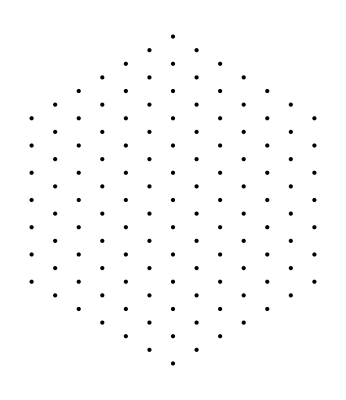

```mathematica
n=6;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G[θ_]:=Join[ArrayFlatten[Table[(n-i)gg5[ θ]+j gg1[ θ],{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)gg5[ θ]+j gg1[ θ],{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G[1]]]
```

```mathematica
HBHZT[{kx,ky}+G[TA][[1]],M]
```

{{10.+M+1.238 ((kx-π^2/3)^2+(ky+π^2/(3 √3))^2),0.+0.365 (kx-π^2/3+ⅈ (ky+π^2/(3 √3))),0,0},{0.+0.365 (kx-π^2/3-ⅈ (ky+π^2/(3 √3))),10.-M-0.174 ((kx-π^2/3)^2+(ky+π^2/(3 √3))^2),0,0},{0,0,10.+M+1.238 ((-kx+π^2/3)^2+(ky+π^2/(3 √3))^2),0.+0.365 (-kx+π^2/3+ⅈ (ky+π^2/(3 √3)))},{0,0,0.+0.365 (-kx+π^2/3-ⅈ (ky+π^2/(3 √3))),10.-M-0.174 ((-kx+π^2/3)^2+(ky+π^2/(3 √3))^2)}}

```mathematica
HInt=Normal@BlockDiagonalMatrix@ParallelTable[ HBHZT[{kx,ky}+G[TA][[i]],M],{i,1,Total@Glength}];
```

```mathematica
diagH[{kxx_,kyy_},dd_]:=N@Chop@HInt/.{kx->kxx,ky->kyy,M->dd}
```

```mathematica
{off1=ConstantArray[0,{Total@Glength,Total@Glength}];Table[off1[[i,i+1]]=1;,{j,1,2n+1},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}
```

{Null}

```mathematica
{off2=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off2[[i,i+Glength[[j]]+1]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off2[[i,i+Glength[[j]]]]=1;,{j,n+1,2n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}
```

{Null}

```mathematica
{off3=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off3[[i,i+Glength[[j]]]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off3[[i,i+Glength[[j]]-1]]=1;,{j,n+1,2n},{i,Gbegin[[j]]+1,Gbegin[[j]]+Glength[[j]]-1}];}
```

{Null}

```mathematica
Hinterationn[V_]:=DiagonalMatrix[{0V,V,0V,V}];diaH[V_]:=Chop@N@KroneckerProduct[off1+off2+off3+Transpose@off1+Transpose@off2+Transpose@off3,Hinterationn[V]]
```

```mathematica
TotalHam3[{kx_,ky_},m_,V_]:=Chop[N[diagH[{kx,ky},m]+diaH[V]]];
```

```mathematica
dim=Dimensions[TotalHam3[{0,0},0.5,0]][[1]]
```

508

```mathematica
rang=Flatten[Table[4j+i,{j,0,Total[Glength]-1},{i,1,2}]];
```

```mathematica
um0=Table[0,{i,1,dim}];
```

```mathematica
UM=Table[ReplacePart[um0,i->1],{i,rang}];
```

```mathematica
HIntHalf=UM.TotalHam3[{kx,ky},m,v].Transpose[UM];
```

```mathematica
TotalHam3half[{kxx_,kyy_},mm_,vv_]:=HIntHalf/.{kx->kxx,ky->kyy,m->mm,v->vv};
```

#### dispersion and phase diagram

```mathematica
M0=0.135;v0=0.089;
```

```mathematica
mkK= {TA 4 π/3, 0};mkM=TA{π,-π/(√3)};mkG={0,0};
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

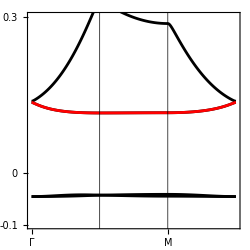

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
M0=0.135;v0=0.094;
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

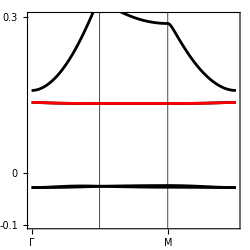

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
M0=0.135;v0=0.054;
```

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4-4,dim/4+4}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p10=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,GridLines->{{101,201},{}},FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black],GridLinesStyle->Directive[Black]];temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3half[k,M0,v0],{dim/4+1}], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p11=ListLinePlot[temp-10,PlotRange->{-0.2,0.6},Frame->True,PlotStyle->Red,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.5,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]];
```

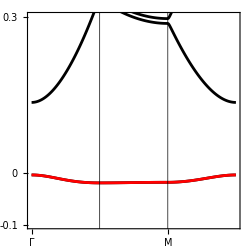

```mathematica
Show[{p10,p11},ImageSize->250,PlotRange->{-0.1,0.3},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"}]
```

```mathematica
numk=30;B1=gg2[TA];B2=gg3[TA];
```

```mathematica
kspace=Flatten[Table[x/numk B1+y/numk B2,{x,0,numk},{y,0,numk}],1]//DeleteDuplicates//N;
```

```mathematica
Graphics@Point@kspace
```

```mathematica
gapandw[{m_,v_}]:=Transpose@ParallelTable[Eigenvalues[TotalHam3half[k,m,v],{dim/4-(0-1)-1,dim/4-(0-1)+1}],{k,kspace}];
```

```mathematica
Getgapandw[t_List]:=With[{t1=t[[1]],t2=t[[2]],t3=t[[3]]},{Min[t1-t2],Min[t2-t3],Max[t2]-Min[t2]}]
```

```mathematica
num2=70
```

```mathematica
parameterspace=Flatten[Table[{M,v},{v,0.0005,0.1,0.1/num2},{M,-0.07,0.12,0.12/num2}],1];
```

```mathematica
Result=Map[Getgapandw,Table[gapandw[para],{para,parameterspace}]]
```

```mathematica
parameterspacelarge=Flatten[Table[{M,v},{v,0.0005,0.12,0.1/num2},{M,-0.07,0.14,0.12/num2}],1];
```

```mathematica
parameterspaceaddition2=Complement[parameterspacelarge,parameterspace];
```

```mathematica
Resultaddition2=Map[Getgapandw,Table[gapandw[para],{para,parameterspaceaddition2}]];
```

```mathematica
parameterspaceall2=Join[parameterspace,parameterspaceaddition2];
```

```mathematica
Resultall2=Join[Result,Resultaddition2];
```

```mathematica
ListDensityPlot[Map[Flatten,Transpose[{parameterspace,Result[[;;,1]]}]],ColorFunction->"TemperatureMap", ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[15,Black],LabelStyle->Directive[20,Black]]
```

```mathematica
ListDensityPlot[Map[Flatten,Transpose[{parameterspace,Map[Min,Transpose@{Result[[;;,1]],Result[[;;,2]]}]/Result[[;;,3]]}]],ColorFunction->"TemperatureMap", ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,20],FrameStyle->Directive[15,Black],LabelStyle->Directive[20,Black]]
```

```mathematica
(*phase transition line*)
```

```mathematica
select[a_]:=If[a<=0.00006,-0.01,a]
```

```mathematica
p1=ListContourPlot[Map[Flatten,Transpose[{parameterspaceall2,Map[select,Chop@Resultall2[[;;,2]]]}]],Contours->{0},ContourShading->None,ContourStyle->{{Opacity[1],White,Thickness[0.01/1.5],Dashed}}];
```

```mathematica
p1=ListContourPlot[Map[Flatten,Transpose[{parameterspaceall2,Map[select,Chop@Resultall2[[;;,1]]]}]],Contours->{0},ContourShading->None,ContourStyle->{{Opacity[1],White,Thickness[0.01/1.5],Dashed}}];
```

## Berry curvature and quantum metric

```mathematica
TotalHam3halfdxint=D[TotalHam3half[{kx,ky},M,v],kx];TotalHam3halfdyint=D[TotalHam3half[{kx,ky},M,v],ky]; TotalHam3halfdx[{kxx_,kyy_}]:=TotalHam3halfdxint/.{kx->kxx,ky->kyy};TotalHam3halfdy[{kxx_,kyy_}]:=TotalHam3halfdyint/.{kx->kxx,ky->kyy};
```

```mathematica
Eigsymhalf[k_List,M_,v_]:=Eigensystem[TotalHam3half[k,M,v]];Sumvb1=Delete[Table[i,{i,1,Dimensions[Eigsymhalf[{0,0},0.135,0.094][[1]]]//First}],nvb1];nvb1=dim/4-(0-1);
```

```mathematica
EigSYMHalf[{kx_,ky_}]:=Eigsymhalf[{0,0},0.135,0.094]
```

```mathematica
FBmatrix[{kx_,ky_}]:=With[{wave=EigSYMHalf[{kx,ky}][[2]],en=EigSYMHalf[{kx,ky}][[1]]},Total@Table[{(Abs[(Conjugate[wave[[nvb1]]].TotalHam3halfdx[{kx,ky}].wave[[i]])]^2+Abs[(Conjugate[wave[[nvb1]]].TotalHam3halfdy[{kx,ky}].wave[[i]])]^2)/(en[[i]]-en[[nvb1]])^2,-2Im@((Conjugate[wave[[nvb1]]].TotalHam3halfdx[{kx,ky}].wave[[i]])(Conjugate[wave[[i]]].TotalHam3halfdy[{kx,ky}].wave[[nvb1]]))/(en[[i]]-en[[nvb1]])^2},{i,Sumvb1}]]
```

```mathematica
FBmatrixALL=ParallelTable[FBmatrix[k],{k,KspaceBZ}];
```

## Wannier function

### ham

```mathematica
b1moire=gg1[ TA];
```

```mathematica
b2moire=gg6[TA];
```

```mathematica
a1moire=Flatten[{x,y}/.Solve[{{x,y}.b1moire==2Pi,{x,y}.b2moire==0},{x,y}]]
```

{18/π,-(18 √3)/π}

```mathematica
a2moire=Flatten[{x,y}/.Solve[{{x,y}.b1moire==0,{x,y}.b2moire==2Pi},{x,y}]]
```

{-36/π,0}

```mathematica
ra=1/3(a1moire-a2moire);
```

```mathematica
ra
```

{18/π,-(6 √3)/π}

```mathematica
ra=1/3(-a1moire-2a2moire)
```

{18/π,(6 √3)/π}

```mathematica
Solve[RotationMatrix[2Pi/6].ra==x a1moire+y a2moire,{x,y}]
```

{{x→-2/3,y→-1/3}}

```mathematica
unitcell=Graphics[Line[Table[RotationMatrix[2Pi/6J].ra,{J,0,6,1}]]];
```

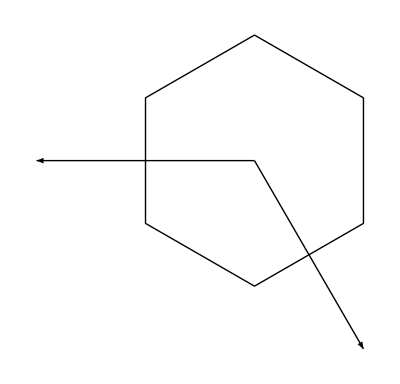

```mathematica
Show[Graphics[{Arrow[{{0,0},a1moire}],Arrow[{{0,0},a2moire}]}],unitcell]
```

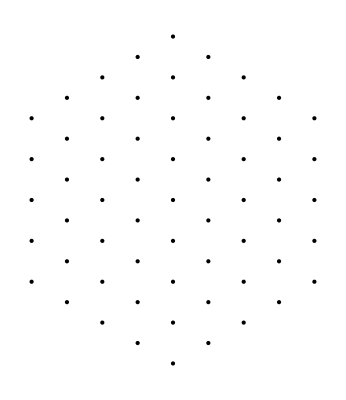

```mathematica
n=4;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G[θ_]:=Join[ArrayFlatten[Table[(n-i)gg5[ θ]+j gg1[ θ],{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)gg5[ θ]+j gg1[ θ],{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G[1]]]
```

```mathematica
solveglist[g_List]:=Flatten[{i,j}/.Solve[i b1moire+j b2moire==g,{i,j}]]
```

```mathematica
G[TA][[1]]
```

{-(2 π^2)/9,(2 π^2)/(9 √3)}

```mathematica
glist=Map[solveglist,G[TA]];
```

```mathematica
glist//Dimensions
```

{61,2}

```mathematica
Glength//Total
```

61

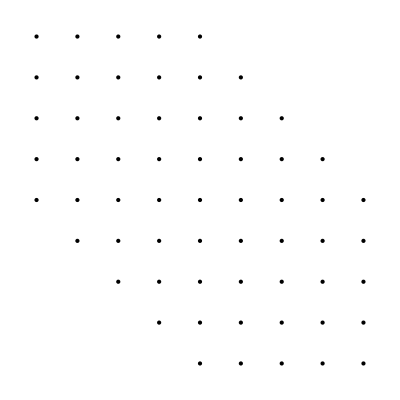

```mathematica
Graphics@Point@glist
```

```mathematica
HInt=Normal@BlockDiagonalMatrix@ParallelTable[ HBHZT[{kx,ky}+G[TA][[i]],M],{i,1,Total@Glength}];
```

```mathematica
HInt//Dimensions
```

{244,244}

```mathematica
diagH[{kxx_,kyy_},dd_]:=N@Chop@HInt/.{kx->kxx,ky->kyy,M->dd}
```

```mathematica
{off1=ConstantArray[0,{Total@Glength,Total@Glength}];Table[off1[[i,i+1]]=1;,{j,1,2n+1},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];};{off2=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off2[[i,i+Glength[[j]]+1]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off2[[i,i+Glength[[j]]]]=1;,{j,n+1,2n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];};
{off3=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off3[[i,i+Glength[[j]]]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off3[[i,i+Glength[[j]]-1]]=1;,{j,n+1,2n},{i,Gbegin[[j]]+1,Gbegin[[j]]+Glength[[j]]-1}];};
```

```mathematica
Hinterationn[V_,l_]:=DiagonalMatrix[{ l V,V,l V,V}];diaH[V_,l_]:=Chop@N@KroneckerProduct[off1+off2+off3+Transpose@off1+Transpose@off2+Transpose@off3,Hinterationn[V,l]]
```

```mathematica
TotalHam3[{kx_,ky_},m_,V_,l_]:=Chop[N[diagH[{kx,ky},m]+diaH[V,l]]];
```

```mathematica
dim=Dimensions[TotalHam3[{kx,ky},m,V,l]]//First
```

244

```mathematica
um0=Table[0,{i,1,dim}];
rang=Flatten[Table[4j+i,{j,0,Total[Glength]-1},{i,1,2}]];
UM=Table[ReplacePart[um0,i->1],{i,rang}];
```

```mathematica
HIntHalf=UM.TotalHam3[{kx,ky},m,v,l].Transpose[UM];
```

```mathematica
mkK= {TA 4 π/3, 0};mkM=TA{π,-π/(√3)};mkG={0,0};
```

```mathematica
TotalHam3half[{kxx_,kyy_},mm_,vv_,ll_]:=HIntHalf/.{kx->kxx,ky->kyy,m->mm,v->vv,l->ll};
```

```mathematica
nflatband=TotalHam3half[{0,0},0.12,0.077]//Dimensions//First
```

122

```mathematica
temp=Transpose@ParallelTable[Part[Sort@Eigenvalues[TotalHam3half[k,0.13,0.08,1]],nflatband/2;;nflatband/2+2], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];
```

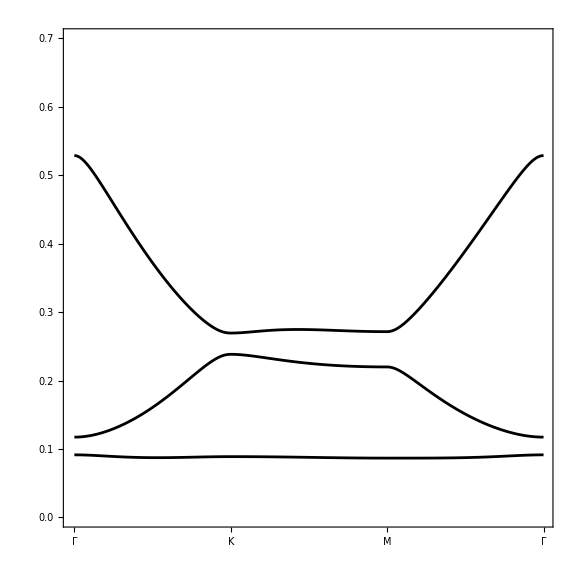

```mathematica
P0=ListLinePlot[temp-10,PlotRange->{0,0.7},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]]
```

```mathematica
temp=Transpose@ParallelTable[Part[Sort@Eigenvalues[TotalHam3half[k,0.135,0.094,0]],nflatband/2-4;;nflatband/2+2], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];
```

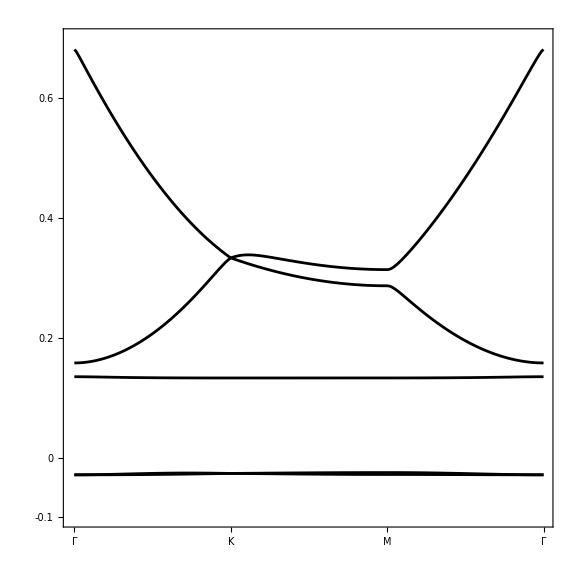

```mathematica
P0=ListLinePlot[temp-10,PlotRange->{-0.1,0.7},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.2,0.4,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]]
```

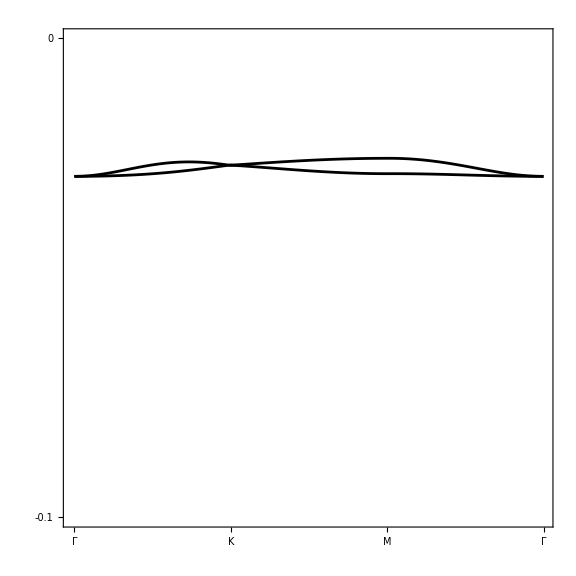

```mathematica
ListLinePlot[temp-10,PlotRange->{-0.1,0},Frame->True,PlotStyle->Black,Frame -> True, ImageSize -> Large, AspectRatio ->1,PlotStyle->Black,FrameTicks->{{{-0.1,0,0.3,0.4,0.6},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,18],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[18,Black]]
```

### Wannier construct

```mathematica
styletext=Directive[Black,FontFamily->"Times New Roman",FontSize->Large]; styleframe={Frame->True,LabelStyle->styletext,FrameTicksStyle->styletext,FrameStyle->Directive[Black,Thickness[Medium]],ImageSize->Medium};
```

```mathematica
wannier90path=FileNameJoin[{NotebookDirectory[],"wannier90-3.1.0_windows_x64_parallel","wannier90","wannier90.x"}];
datafolder=FileNameJoin[{NotebookDirectory[],"E3c"}];
dataname="e3c";
```

```mathematica
a1=a1moire*TA;
a2=a2moire*TA;
b1=b1moire/TA;
b2=b2moire/TA;
```

```mathematica
parameters=Association["num_band"->3,
"num_wann"->1,
"num_iter"->400,
"unit_cell_cart"->{Append[0][a1],Append[0][a2],{0,0,20Norm@a1}},
"atoms_frac"->{{"C1",0,0,0}},
"projections"->{"C1:s"},
"mp_grid"->{16,16,1},
"write_u_matrices"->True
];
```

```mathematica
kpoints=N@Divide[#,parameters["mp_grid"]]&/@Flatten[Array[List,parameters["mp_grid"]]-1,2];
trialorbitals={{{0,0},Normalize@{0,1}}};
```

```mathematica
kpoints[[2]]
```

{0.,0.0625,0.}

```mathematica
numband1=0;numband2=2;
utG[g_List]:=utG[g]=ArrayFlatten@Outer[If[(#1-g)==#2,IdentityMatrix[2],0*IdentityMatrix[2]]&,glist,glist,1];
```

```mathematica
utG[glist[[1]]/2]//Dimensions
```

{122,122}

```mathematica
datafolder
```

C:\Users\15521\OneDrive\Desktop\heavy fermion bhz\heavy fermion bhz\E3c

```mathematica
file=FileNameJoin[{datafolder,dataname<>".win"}];
WriteLine[file,"!test \n"];

WriteLine[file,"num_wann = "<>ToString@parameters["num_wann"]];WriteLine[file,"num_bands = "<>ToString@parameters["num_band"]];
WriteLine[file,"num_iter = "<>ToString@parameters["num_iter"]];
WriteLine[file,"write_u_matrices = "<>ToString@parameters["write_u_matrices"]]

WriteLine[file,"\n! SYSTEM \n"];

WriteLine[file,"begin unit_cell_cart"];
WriteLine[file,ExportString[Map[NumberForm[N@#,{10,5}]&,parameters["unit_cell_cart"],{2}],"Table","FieldSeparators"->" "]];
WriteLine[file,"end unit_cell_cart\n"];

WriteLine[file,"begin atoms_frac"];
WriteLine[file,ExportString[Map[NumberForm[N@#,{10,5}]&,parameters["atoms_frac"],{2}],"Table","FieldSeparators"->" "]];
WriteLine[file,"end atoms_frac\n"];

WriteLine[file,"begin projections"];
WriteLine[file,ExportString[parameters["projections"],"Table","FieldSeparators"->" "]];
WriteLine[file,"end projections\n"];

WriteLine[file,"!KPPOINTS\n"];
WriteLine[file,"mp_grid = "<>ExportString[{parameters["mp_grid"]},"Table","FieldSeparators"->" "]];

WriteLine[file,"begin kpoints"];
WriteLine[file,ExportString[Map[NumberForm[N@#,{10,5}]&,kpoints,{2}],"Table","FieldSeparators"->" "]];
WriteLine[file,"end kpoints\n"];

Close[file];
```

```mathematica
RunProcess[{wannier90path,"-pp",dataname},ProcessDirectory->datafolder]
```

<|ExitCode→0,StandardOutput→,StandardError→|>

```mathematica
mesh=Association@Table[
Rule[First@#,ToExpression@StringSplit@Rest[Most@#]]&@StringSplit[section,"\r\n"],{section,StringSplit[ReadString[FileNameJoin[{datafolder,dataname<>".nnkp"}]],"begin"~~_]}];
```

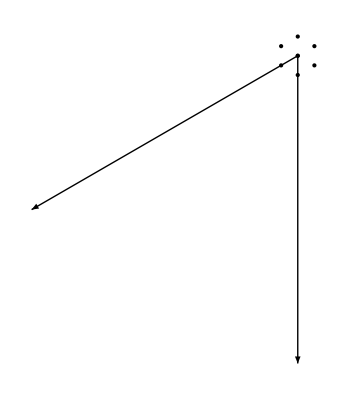

```mathematica
(*check nearest neighbors*)
Graphics[{Point[
(Most[kpoints⟦#⟦2⟧⟧].{b1moire,b2moire}+#⟦3⟧*b1moire+#⟦4⟧*b2moire)&/@Cases[mesh["nnkpts"],{1,___}]
],Arrow[{{{0,0},b1moire},{{0,0},b2moire}}]}]
```

```mathematica
blochwavefunctions=Table[Part[Sort@Transpose@Eigensystem[TotalHam3half[Most[k].{b1moire,b2moire},0.135,0.094,0]],nflatband/2;;nflatband/2+2,2],{k,kpoints}];
```

```mathematica
energy=Table[Part[Sort@Transpose@Eigensystem[TotalHam3half[Most[k].{b1moire,b2moire},0.135,0.094,0]],nflatband/2;;nflatband/2+2,1],{k,kpoints}];
```

```mathematica
energy[[1]]-10
```

{0.135,0.158031,0.681323}

```mathematica
kpoints//Dimensions
```

{256,3}

```mathematica
kpoints//Max
```

0.9375

```mathematica
energy[[2]]
```

{10.1348,10.1605,10.629}

```mathematica
blochwavefunctions//Dimensions
```

{256,3,122}

```mathematica
overlaps=Table[{{deltak},
ReIm@Flatten@Transpose@Outer[Dot,Conjugate@blochwavefunctions⟦deltak⟦1⟧⟧,If[Last@deltak==0,utG[{deltak⟦3⟧,deltak⟦4⟧}]†,IdentityMatrix[2*Length@glist]].#&/@blochwavefunctions⟦deltak⟦2⟧⟧,1]
},{deltak,Rest@mesh["nnkpts"]}]~Flatten~2;
```

```mathematica
overlaps//Dimensions
```

{20480}

```mathematica
projections2=Table[{Partition[Tuples[{Range@parameters["num_band"],Range@parameters["num_wann"],{i}}],parameters["num_wann"]],
ReIm@Dot[Conjugate[blochwavefunctions⟦i⟧],Table[Exp[-ⅈ (Most@kpoints⟦i⟧+g).{b1moire,b2moire}.orbital⟦1⟧]*orbital⟦2⟧,{orbital,trialorbitals},{g,glist}]~Flatten~{{2,3},{1}}]
}~Flatten~{{3},{2},{1,4}},{i,1,Length@kpoints}]~Flatten~2;
```

```mathematica
file=FileNameJoin[{datafolder,dataname<>".mmn"}];
WriteLine[file,"!overlaps"];

WriteLine[file,ExportString[{{parameters["num_band"],mesh["kpoints"]⟦1,1⟧,mesh["nnkpts"]⟦1,1⟧}},"Table","FieldSeparators"->" "]];

WriteLine[file,ExportString[Map[If[IntegerQ@#,#,NumberForm[DecimalForm@N@#,{10,10}]]&,overlaps,{2}],"Table","FieldSeparators"->" "]];

Close[file];

file=FileNameJoin[{datafolder,dataname<>".amn"}];
WriteLine[file,"!projection"];

WriteLine[file,ExportString[{{parameters["num_band"],mesh["kpoints"]⟦1,1⟧,parameters["num_wann"]}},"Table","FieldSeparators"->" "]];

WriteLine[file,ExportString[Map[If[IntegerQ@#,#,NumberForm[DecimalForm@N@#,{10,10}]]&,projections2,{2}],"Table","FieldSeparators"->" "]];

Close[file];
```

```mathematica
Eig=Flatten[Table[MapThread[Append,{Table[{i,j},{i,1,3}],energy[[j]]}],{j,mesh["kpoints"]⟦1,1⟧}],1];
```

```mathematica
Eig//Dimensions
```

{768,3}

```mathematica
file=FileNameJoin[{datafolder,dataname<>".eig"}];


WriteLine[file,ExportString[Map[If[IntegerQ@#,#,NumberForm[DecimalForm@N@#,{10,10}]]&,Eig,{2}],"Table","FieldSeparators"->" "]];

Close[file];
```

```mathematica
RunProcess[{wannier90path,dataname},ProcessDirectory->datafolder]
```

<|ExitCode→0,StandardOutput→,StandardError→|>

### plot

```mathematica
wanniertransform2={ToExpression@StringSplit@First@#,Transpose@Partition[Complex@@@ToExpression@StringSplit@Rest@#,parameters["num_wann"]]}&/@Rest@StringSplit[StringSplit[ReadString[FileNameJoin[{datafolder,dataname<>"_u.mat"}]],"\r\n\r\n"],"\r\n"];
```

```mathematica
wanniertransform={ToExpression@StringSplit@First@#,Transpose@Partition[Complex@@@ToExpression@StringSplit@Rest@#,parameters["num_wann"]]}&/@Rest@StringSplit[StringSplit[ReadString[FileNameJoin[{datafolder,dataname<>"_u_dis.mat"}]],"\r\n\r\n"],"\r\n"];
```

```mathematica
totaltansform=Table[wanniertransform2[[i,2,1,1]] wanniertransform[[i,2]],{i,1,256}];
```

```mathematica
wannierwave=Flatten[wanniertransform2[[All,2]]]MapThread[Dot,{wanniertransform[[All,2]],blochwavefunctions}];WannierwaveR2[{Rx_,Ry_}]:=N@Total[Exp[ -I ((Most/@kpoints).{b1moire,b2moire}).{Rx,Ry}]*  wannierwave];RList=Flatten[Table[m a1moire+mm a2moire,{m,-80,80},{mm,-80,80}],1];
```

```mathematica
WannierwaveK2[{kx_,ky_}]:=Total@ParallelTable[Exp[I {kx,ky}.R]WannierwaveR2[R],{R,RList}];
```

```mathematica
wavekn[K_List]:=Part[Sort@Transpose@Eigensystem[TotalHam3half[K,0.135,0.094,0]],nflatband/2;;nflatband/2+2,2];

dk=0.05;

klist0= Join[Table[λ mkK, {λ, 0, 1, dk}], Table[mkK+ λ (mkM- mkK), {λ,dk, 1, dk}], Table[mkM+ λ (mkG-mkM), {λ,dk, 1, dk}]]
klist=Join[{1,Table[2i,{i,1,30,1}],61}]//Flatten

result1=Table[With[{t=Normalize@WannierwaveK2[k][[1]]},Table[Conjugate[wavekn[k][[i]]].t,{i,1,3}]]//Abs//Chop,{k,klist0[[klist]]}]
```

```mathematica
overlap2=Map[Normalize,result1];
```

```mathematica
Eall=ParallelTable[Part[Sort@Transpose@Eigensystem[TotalHam3half[k,0.135,0.094,0]],nflatband/2;;nflatband/2+2,1], {k,klist0[[klist]]}]
```

```mathematica
f[a_,b_,c_]:=Graphics[{Red,PointSize[c/50],Point[{a,b}]}]
```

```mathematica
axix0=Table[{1+dk/0.01i,1+dk/0.01i,1+dk/0.01i},{i,0,(Eall//Dimensions//First)-1}];
```

```mathematica
axix=axix2[[klist]]
```

```mathematica
result00=Table[MapThread[f,Transpose[{axix,Eall2-10,overlap3}][[i]]],{i,1,First@Dimensions@axix}]//Flatten
```

```mathematica
Show[P0,result00,ImageSize->250,PlotRange->{0,0.7},Framed->True,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"},GridLines->{{101,201},{}}]
```

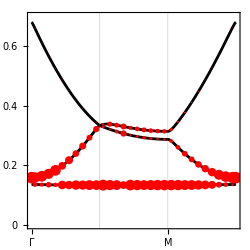

```mathematica
wannierR0[r_List]:=Total@Partition[#,2]&/@Total[
Flatten[wanniertransform2[[All,2]]]MapThread[Dot,{
(wanniertransform⟦All,2⟧),
blochwavefunctions*(ConstantArray[Outer[Times,Exp[ⅈ 2π(Most/@kpoints).r],Exp[ⅈ 2π glist.r]],{parameters["num_band"],2}]~Flatten~{{3},{1},{4,2}})
}]
]/Length@kpoints;
```

```mathematica
wannierR0r=ParallelTable[{{rx,ry}.{a1moire,a2moire},(Norm/@wannierR0[{rx,ry}])^2},{rx,-1.8,1.8,1/10},{ry,-1.8,1.8,1/10}]~Flatten~{{1,2},{3,4}};
```

```mathematica
P0=Show[ListDensityPlot[Extract[wannierR0r,{All,{1,2,3}}],PlotRange->{{-0.8Norm@a1moire,0.8Norm@a1moire},{-0.8Norm@a1moire,0.8Norm@a1moire},All},PlotLegends->Automatic,ColorFunction->"SunsetColors"],Graphics[{Opacity[0],EdgeForm[{White,Thick}],Polygon[NestList[Dot[RotationMatrix[π/3],#]&,2/3*a1moire+1/3*a2moire,6]]}]
]
```

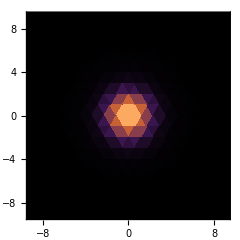

## raw data input for phase diagram

```mathematica
pphase=
```

#### plot

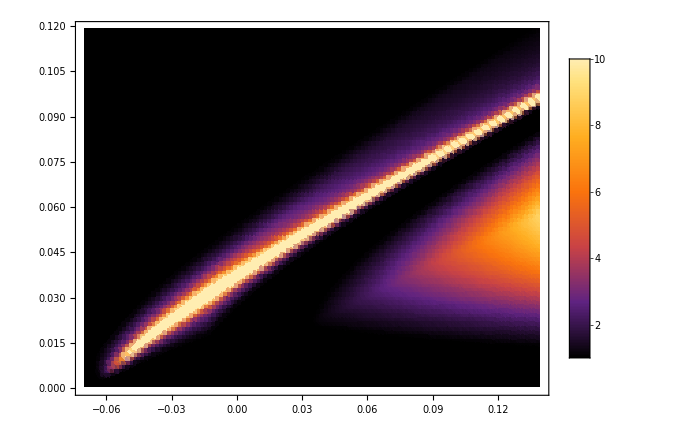

```mathematica
PWDD=ListDensityPlot[pphase,ColorFunction->(ColorData["SunsetColors"]@(0.9*Rescale[#,{1,10}])&),ColorFunctionScaling->False, ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[15,Black],PlotRange->{1,10},ClippingStyle->Automatic]
```

# Fig3

# Fig4